```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}]; 
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

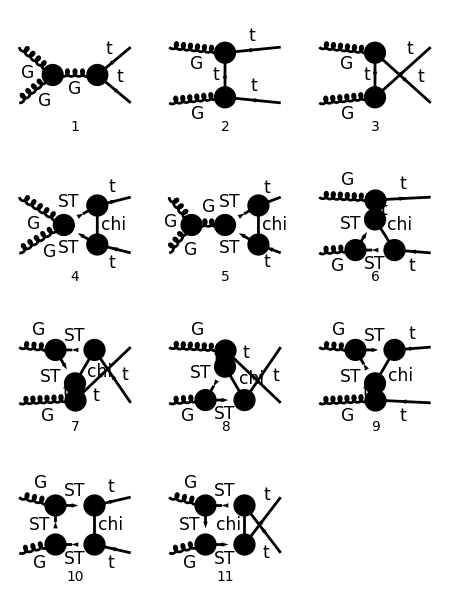

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
(* goodDiags=DiagramExtract[goodDiags,{1,5}]; *)
(* goodDiags=DiagramExtract[goodDiags,{10,11}]; *) 
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 450,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True, SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},TransversePolarizationVectors->{k1,k2}, LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames->{μ,ν}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]];
(* Remove terms of higher order *)
ampB = Normal[Series[ampB,{yDM,0,2},{gs,0,2}]];
```

in total: 2 Particles amplitudes

```mathematica
ampC =Simplify[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True])];
```

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampD=Simplify[ampC-ampSM];
(* ampD=ampD/.{PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C00,PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C11,PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C12,PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},a__]->C1}; *)
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=Simplify[DiracSimplify[ampD]];
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp,PaVe]]}];
```

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp,deltaCTR]] (-1/(4 EpsilonUV));
FullSimplify[loopUV+ctUV]
```

0

## Tensor Structure

```mathematica
PVsubs =Flatten[Table[PaVe[a,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a],ToString[b]]],{a,0,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[b]]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{0,b,MT^2,s,MT^2,-2MT^2+s+t+u},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],ToString[b]]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
```

```mathematica
ampEsimp2=DiracSimplify[ampEsimp/.PVsubs/.{DiracGamma[7]->1-DiracGamma[6]}];
```

```mathematica
pairs=Cases2[ampEsimp2,Pair]
sps=Cases2[ampEsimp2,Spinor]
gams=Cases2[ampEsimp2,DiracGamma]
allTerms=Join[Table[sps[[1]].gams[[i]].sps[[2]],{i,Length[gams]}],Flatten[Table[sps[[1]].gams[[i]].gams[[j]].sps[[2]],{i,Length[gams]},{j,Length[gams]}]]];
```

{k2·ε(k1),p1·ε(k1),p1·ε(k2),p2·ε(k1),p2·ε(k2),ε(k1)·ε(k2)}

{φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,γ·k2,γ·ε(k1),γ·ε(k2)}

```mathematica
ampEsimp3=Collect[ampEsimp2,allTerms,FullSimplify]
```

4 ⅈ gs^2 π^2 (φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) ((p2·ε(k2)) ((D002t+D003t) (T^Glu1 T^Glu2)_Col3Col4-D003u (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k2)) (D003t (T^Glu1 T^Glu2)_Col3Col4-(D002u+D003u) (T^Glu2 T^Glu1)_Col3Col4)) yDM^2+2 ⅈ gs^2 π^2 (φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) ((k2·ε(k1)) ((2 D001t+D00t) (T^Glu1 T^Glu2)_Col3Col4-(2 D001u+D00u) (T^Glu2 T^Glu1)_Col3Col4)+(p2·ε(k1)) ((2 (D002t+D003t)+D00t) (T^Glu1 T^Glu2)_Col3Col4-(2 D003u+D00u) (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k1)) ((2 D003t+D00t) (T^Glu1 T^Glu2)_Col3Col4-(2 (D002u+D003u)+D00u) (T^Glu2 T^Glu1)_Col3Col4)) yDM^2+2 ⅈ gs^2 π^2 (φ(p1,MT)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (((p1·ε(k1)) ((2 D133t+D13t) (p1·ε(k2))+(2 D123t+D12t+2 D133t+D13t) (p2·ε(k2)))+(p2·ε(k1)) ((2 (D123t+D133t)+D13t) (p1·ε(k2))+(2 D122t+4 D123t+D12t+2 D133t+D13t) (p2·ε(k2)))+2 D001t (ε(k1)·ε(k2))) (T^Glu1 T^Glu2)_Col3Col4-((p2·ε(k1)) ((2 D123u+D12u+2 D133u+D13u) (p1·ε(k2))+(2 D133u+D13u) (p2·ε(k2)))+(p1·ε(k1)) ((2 D122u+4 D123u+D12u+2 D133u+D13u) (p1·ε(k2))+(2 (D123u+D133u)+D13u) (p2·ε(k2)))+2 D001u (ε(k1)·ε(k2))) (T^Glu2 T^Glu1)_Col3Col4+(k2·ε(k1)) ((p2·ε(k2)) ((2 D112t+2 D113t+D12t+D13t) (T^Glu1 T^Glu2)_Col3Col4-(2 D113u+D13u) (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k2)) ((2 D113t+D13t) (T^Glu1 T^Glu2)_Col3Col4-(2 D112u+2 D113u+D12u+D13u) (T^Glu2 T^Glu1)_Col3Col4))) yDM^2-2 ⅈ gs^2 MT π^2 (φ(p1,MT)).(φ(-p2,MT)) (((p2·ε(k1)) ((2 D223t+4 D233t+3 D23t+2 D333t+3 D33t+D3t) (p1·ε(k2))+(2 D222t+6 D223t+3 D22t+6 D233t+6 D23t+D2t+2 D333t+3 D33t+D3t) (p2·ε(k2)))+2 (D002t+D003t+D00t) (ε(k1)·ε(k2))) (T^Glu1 T^Glu2)_Col3Col4-((p2·ε(k1)) ((2 D233u+D23u+2 D333u+D33u) (p1·ε(k2))+(2 D333u+D33u) (p2·ε(k2)))+2 D003u (ε(k1)·ε(k2))) (T^Glu2 T^Glu1)_Col3Col4+(k2·ε(k1)) ((p2·ε(k2)) ((2 D122t+4 D123t+2 D12t+2 D133t+2 D13t+D22t+2 D23t+D2t+D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D133u+D33u) (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k2)) ((2 D123t+2 D133t+2 D13t+D23t+D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D123u+2 D133u+D23u+D33u) (T^Glu2 T^Glu1)_Col3Col4))+(p1·ε(k1)) ((p1·ε(k2)) ((2 D233t+D23t+2 D333t+3 D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D223u+4 D233u+D23u+2 D333u+D33u) (T^Glu2 T^Glu1)_Col3Col4)+(p2·ε(k2)) ((2 D223t+D22t+4 D233t+4 D23t+D2t+2 D333t+3 D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 (D233u+D333u)+D33u) (T^Glu2 T^Glu1)_Col3Col4))) yDM^2+2 ⅈ gs^2 MT π^2 (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (((p2·ε(k1)) ((2 D223t+6 D233t+3 D23t+4 (D333t+D33t)+D3t) (p1·ε(k2))+(2 D222t+8 D223t+3 D22t+10 D233t+7 D23t+D2t+4 (D333t+D33t)+D3t) (p2·ε(k2)))+2 (D002t+2 D003t+D00t) (ε(k1)·ε(k2))) (T^Glu1 T^Glu2)_Col3Col4-((p2·ε(k1)) ((2 D223u+D22u+6 D233u+5 D23u+D2u+4 (D333u+D33u)+D3u) (p1·ε(k2))+(2 D233u+D23u+4 (D333u+D33u)+D3u) (p2·ε(k2)))+2 (D002u+2 D003u+D00u) (ε(k1)·ε(k2))) (T^Glu2 T^Glu1)_Col3Col4+(k2·ε(k1)) ((p2·ε(k2)) ((2 D122t+6 D123t+2 D12t+4 D133t+2 D13t+D22t+3 D23t+D2t+2 D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D123u+4 D133u+2 D13u+D23u+2 D33u+D3u) (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k2)) ((2 D123t+4 D133t+2 D13t+D23t+2 D33t+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D122u+6 D123u+2 D12u+4 D133u+2 D13u+D22u+3 D23u+D2u+2 D33u+D3u) (T^Glu2 T^Glu1)_Col3Col4))+(p1·ε(k1)) ((p2·ε(k2)) ((2 D223t+D22t+6 D233t+5 D23t+D2t+4 (D333t+D33t)+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D223u+6 D233u+3 D23u+4 (D333u+D33u)+D3u) (T^Glu2 T^Glu1)_Col3Col4)+(p1·ε(k2)) ((2 D233t+D23t+4 (D333t+D33t)+D3t) (T^Glu1 T^Glu2)_Col3Col4-(2 D222u+8 D223u+3 D22u+10 D233u+7 D23u+D2u+4 (D333u+D33u)+D3u) (T^Glu2 T^Glu1)_Col3Col4))) yDM^2

```mathematica
Cases2[ampEsimp,FeynAmpDenominator]
```

{}

```mathematica
allTerms[[1]]
```

(φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))

```mathematica
Collect[Coefficient[ampEsimp2,allTerms[[1]]],pairs,Simplify]
```

-2 ⅈ gs^2 MT π^2 (p2·ε(k1)) (p2·ε(k2)) ((C_0(MT^2,t,0,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+((C_1(MT^2,t,0,mST^2,mChi^2,mST^2)+3 C_2(MT^2,t,0,mST^2,mChi^2,mST^2)+2 (C_12(MT^2,t,0,mST^2,mChi^2,mST^2)+C_22(MT^2,t,0,mST^2,mChi^2,mST^2))) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 D_223(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-4 D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+3 D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+2 D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4) yDM^2+gs^2 MT π^2 (p1·ε(k2)) (p2·ε(k1)) (2 ⅈ (D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(C_2(MT^2,u,0,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4+(2 C_12(MT^2,u,0,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 C_22(MT^2,u,0,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-3 D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)-(2 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2) yDM^2+gs^2 MT π^2 (ε(k1)·ε(k2)) (((t-u) (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-ⅈ (-4 D_003(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 (D_00(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+D_002(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+D_003(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)) (T^Glu2 T^Glu1)_Col3Col4+C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))) yDM^2+(k1·ε(k2)) ((gs^2 MT π^2 yDM^2 (p1·ε(k1)) (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(gs^2 MT π^2 yDM^2 (p2·ε(k1)) (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2)+(p1·ε(k1)) (2 ⅈ gs^2 MT π^2 (p1·ε(k2)) (D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+(-D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+(C_2(MT^2,u,0,mST^2,mChi^2,mST^2)+2 C_22(MT^2,u,0,mST^2,mChi^2,mST^2))/((k2-p1)^2-MT^2)-3 D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-6 D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-3 D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-2 D_222(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-6 D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-6 D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)-2 D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)) (T^Glu2 T^Glu1)_Col3Col4) yDM^2+gs^2 MT π^2 (p2·ε(k2)) ((2 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ C_0(MT^2,t,0,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-1/((k2-p2)^2-MT^2)2 ⅈ (3 C_1(MT^2,t,0,mST^2,mChi^2,mST^2)+3 C_2(MT^2,t,0,mST^2,mChi^2,mST^2)+2 (C_11(MT^2,t,0,mST^2,mChi^2,mST^2)+2 C_12(MT^2,t,0,mST^2,mChi^2,mST^2)+C_22(MT^2,t,0,mST^2,mChi^2,mST^2))) (T^Glu1 T^Glu2)_Col3Col4+2 ⅈ D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 ⅈ D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 ⅈ D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+4 ⅈ D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-2 ⅈ D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-6 ⅈ D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-6 ⅈ D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 ⅈ D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-8 ⅈ D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-4 ⅈ D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4) yDM^2)+(k2·ε(k1)) (gs^2 MT π^2 (p2·ε(k2)) (((C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ C_0(MT^2,t,0,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 ⅈ (C_1(MT^2,t,0,mST^2,mChi^2,mST^2)+3 C_2(MT^2,t,0,mST^2,mChi^2,mST^2)+2 (C_12(MT^2,t,0,mST^2,mChi^2,mST^2)+C_22(MT^2,t,0,mST^2,mChi^2,mST^2))) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+2 ⅈ (D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_123(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4-2 D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu2 T^Glu1)_Col3Col4)) yDM^2+gs^2 MT π^2 (p1·ε(k2)) (2 ⅈ (D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4+2 D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) (T^Glu1 T^Glu2)_Col3Col4-(D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+2 D_12(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+2 D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+(C_2(MT^2,u,0,mST^2,mChi^2,mST^2)+2 C_22(MT^2,u,0,mST^2,mChi^2,mST^2))/((k2-p1)^2-MT^2)+D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+2 D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+2 D_122(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+4 D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)+2 D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2)) (T^Glu2 T^Glu1)_Col3Col4)-((C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2) yDM^2)